Universidad de Jaén. EPS Jaén.
Departamento de Matemáticas. Grado en Ingeniería Informática
Análisis y Métodos Numéricos. 
F. Javier Muñoz Delgado

## Problemas de examen. Tema 11. Interpolación y aproximación polinomial.

## Interpolación polinomial

## 12.- Calcula el polinomio de ℙ_4 que interpola f(0)=1, f ‘(0)=2, f’’(0)=2, f(2)=3, f(3)=2. Enero 18

Solución:
El polinomio de interpolación escrito en la forma de Newton será
	p(x) = A + B x + C x^2+ D x^3+ E x^3(x-2).
Ahora podemos imponer las condiciones de interpolación o aplicar la fórmula de las diferencias divididas.
Si imponemos las condiciones de interpolación:
	p(0)=1 = A
	p’(0)=2=B
	p’’(0)=2=2C
Con esto tenemos p(x) = 1 + 2 x + x^2+ D x^3+ E x^3(x-2).
	p(2)=3=1+4+4+8D; D=-6/8=-3/4
	p(3)=2= 1 + 6 + 9 + (-3/4)  27+ E 27; 2-16+81/4 = 27E;  25/4 = 27E; E=25/108
El polinomio interpolador es:	
	 p(x) = 1 + 2 x + x^2 -(3/4) x^3+ (25/108) x^3(x-2).

## 12.- Calcula el polinomio de ℙ_3 que interpola f(1)=1, f ‘(1)=2, f(2)=1, f ‘(2)=-1. Octubre 18, Julio 18

Solución:
Utilizando la idea de Newton, podríamos escribir el polinomio en la forma 
		p(x) = a + b (x-1) + c (x-1)^2 + d (x-1)^2(x-2).
Los coeficientes a, b, c y d se pueden calcular sustituyendo los datos. Así encontraríamos primero a, y sucesivamente, b, c y d.

También podemos utilizar la ley de recurrencia de las diferencias divididas.
p(x) = f[1] + f[1,1] (x-1) + f[1,1,2] (x-1)^2 + f[1,1,2,2] (x-1)^2 (x-2)

f(1) = f[1] = 1, f[1,1] = f’(1)=2 ,  						f[1,1,2] = (f[1,2]-f[1,1])/(2-1) = (0-2)/(2-1) = -2, 	f[1,1,2,2]=(f[1,2,2]-f[1,1,2])/(2-1)=(-1-(-2))/1=1
f(1) = f[1] = 1, f[1,2] = (f[2]-f[1])/(2-1) = (1-1)/(2-1)=0,	f[1,2,2] = (f[2,2]-f[1,2])/(2-1) = (-1-0)/1=-1
f(2) = f[2] = 1, f[2,2] = f’(2)= -1
f(2) = f[2] = 1

El polinomio que interpola es p(x) =  1 + 2 (x-1) -2 (x-1)^2 + 1 (x-1)^2(x-2)=1 + 2 (x-1) -2 (x-1)^2 +  (x-1)^2(x-2) = -5 + 11x - 6 x^2+ x^3

Con el Mathematica,

```mathematica
InterpolatingPolynomial[{{1,1,2},{2,1,-1}},x]
```

1+(2+(-4+x) (-1+x)) (-1+x)

```mathematica
Collect[%,x]
```

-5+11 x-6 x^2+x^3

## 11.- Calcula el polinomio de ℙ_4 que interpola f(0)=2, f ‘(0)=1, f’’(0)=2, f(2)=3, f ‘(2)=2. Enero 19

Solución:
El polinomio de interpolación escrito en la forma de Newton será
	p(x) = A + B x + C x^2+ D x^3+ E x^3(x-2).
Ahora podemos imponer las condiciones de interpolación o aplicar la fórmula de las diferencias divididas.
Si imponemos las condiciones de interpolación:
	p(0)=2 = A
	p’(0)=1=B
	p’’(0)=2=2C
Con esto tenemos p(x) = 2 + x + x^2+ D x^3+ E x^3(x-2).
	p(2)=3=2+2+4+8D; D=-5/8
Tenemos que p(x) = 2 + x + x^2 -5/8 x^3+ E x^3(x-2).
	p’(x)= 1 + 2 x - 15/8 x^2 + E (4x^3- 6 x^2)
	p’(2)= 2 = 1 + 4 - 15/2 + 8 E ⟹ 9/2= 8E, E=9/16
	p(x) = 2 + x + x^2 -5/8 x^3+ 9/16 x^3(x-2).

## 11.- Calcula el polinomio de ℙ_3 que interpola f(0)=1, f(1)=3, f(2)=6, f(3)=10 mediante el método de las diferencias divididas. Enero 20

Solución:
Datos
f[0]=f(0)=1     f[1,0]=(3-1)/(1-0)=2      f[2,1,0]=(3-2)/(2-0)=1/2    f[3,2,1,0]=(1/2-1/2)/(3-0)=0
f[1]=f(1)=3     f[2,1]=(6-3)/(2-1)=3      f[3,2,1]=(4-3)/(3-1)=1/2
f[2]=f(2)=6     f[3,2]=(10-6)/(3-2)=4
f[3]=f(3)=10
p(x) = f[0] + f[1,0] (x-0) + f[2,1,0] (x-0)(x-1) + f[3,2,1,0] (x-0)(x-1)(x-2) = 1 + 2 (x-0) + 1/2 (x-0)(x-1) + 0 (x-0)(x-1)(x-2) = 1 + 2x  + x^2/2-x/2 = 1+ 3x/2 + x^2/2

## 12.- Calcula el polinomio de ℙ_3 que interpola f(1)=1, f(2)=2, f ‘(2)=-1, f(3)=2. Enero 21

Solución:
Utilizando la idea de Newton, podríamos escribir el polinomio en la forma 
		p(x) = a + b (x-1) + c (x-1) (x-2) + d (x-1) (x-2)^2.
Los coeficientes a, b, c y d se pueden calcular sustituyendo los datos. Así encontraríamos primero a, y sucesivamente, b ,c y d.

También podemos utilizar la ley de recurrencia de las diferencias divididas. 
p(x) = f[1] + f[1,2] (x-1) + f[1,2,2] (x-1) (x-2) + f[1,2,2,3] (x-1) (x-2)^2

f(1) = f[1] = 1, f[1,2] = (f[2]-f[1])/(2-1) = 1 ,  	f[1,2,2] = (f[2,2]-f[1,2])/(2-1) = (-1-1)/1 = -2, 	f[1,2,2,3]=(f[2,2,3]-f[1,2,2])/(3-1)=(1-(-2))/2=3/2
f(2) = f[2] = 2, f[2,2] = f ’(2) = -1,				f[2,2,3] = (f[2,3]-f[2,2])/(3-2) = (0-(-1))/1=1
f(2) = f[2] = 2, f[2,3] = (f[3]- f[2])/(3-2) = 0
f(3) = f[3] = 2

El polinomio que interpola es p(x) =  1 + 1 (x-1) - 2 (x-1) (x-2) + 3/2  (x-1) (x-2)^2=10+19 x-(19 x^2)/2+(3 x^3)/2

## 12.- Calcula el polinomio de ℙ_3 que interpola f(1) = 1, f(2) = 2, f ‘(2)= -1, f ‘’(2) = 3. Febrero 21

Solución:
Utilizando la idea de Newton, podríamos escribir el polinomio en la forma 
		p(x) = a + b (x-1) + c (x-1) (x-2) + d (x-1) (x-2) (x-2).
Los coeficientes a, b, c y d se pueden calcular sustituyendo los datos. Así encontraríamos primero a, y sucesivamente, b, c y d.

También podemos utilizar la ley de recurrencia de las diferencias divididas. 
p(x) = f[1] + f[1,2] (x-1) + f[1,2,2] (x-1) (x-2) + f[1,2,2,2] (x-1) (x-2)(x-2)

f(1) = f[1] = 1, 	f[1,2] = (f[2]-f[1])/(2-1) = 1 ,  	f[1,2,2] = (f[2,2]-f[1,2])/(2-1) = (-1-1)/1 = -2, 	f[1,2,2,2]=(f[2,2,2]-f[1,2,2])/(2-1)=((3/2)-(-2))/1=7/2
f(2) = f[2] = 2, 	f[2,2] = f’(2) = -1,			f[2,2,2] = f’’(2)/2! = 3/2
f(2) = f[2] = 2, 	f[2,2] = f ’(2)= -1
f(2) = f[2] = 2

El polinomio que interpola es p(x) =  1 + 1 (x-1) - 2 (x-1) (x-2) + (7/2)  (x-1) (x-2) (x-2) = -18+35 x -39/2 x^2 + 7/2 x^3
Con el Mathematica:

```mathematica
InterpolatingPolynomial[{{1,1},{2,2,-1,3}},x]
```

1+(1+(-2+7/2 (-2+x)) (-2+x)) (-1+x)

```mathematica
Collect[%,x]
```

-18+35 x-(39 x^2)/2+(7 x^3)/2

## 12.- Calcula el polinomio de ℙ_3 que interpola f(1) = 1, f(2) = 2, f (3)= -1, f ‘(3) = 3. Junio 21

Solución:
Utilizando la idea de Newton, podríamos escribir el polinomio en la forma 
		p(x) = a + b (x-1) + c (x-1) (x-2) + d (x-1) (x-2) (x-3).
Los coeficientes a, b, c y d se pueden calcular sustituyendo los datos. Así encontraríamos primero a, y sucesivamente, b, c y d.

También podemos utilizar la ley de recurrencia de las diferencias divididas. 
p(x) = f[1] + f[1,2] (x-1) + f[1,2,3] (x-1) (x-2) + f[1,2,3,3] (x-1) (x-2)(x-3)

f(1) = f[1] = 1,  f[1,2] = (f[2]-f[1])/(2-1) = 1 ,  	f[1,2,3] = (f[2,3]-f[1,2])/(3-1) = (-3-1)/2 = -2, 	f[1,2,3,3]=(f[2,3,3]-f[1,2,2])/(3-1)=(6-(-2))/2=4
f(2) = f[2] = 2,  f[2,3] = (f[3]-f[2])/(3-2) = -3,	f[2,3,3] = (f[3,3]-f[2,3])/(3-2) = (3-(-3))/(3-2)=6
f(3) = f[3] = -1, f[3,3] = f ’(3)= 3
f(3) = f[3] = -1

El polinomio que interpola es p(x) =  1 + 1 (x-1) - 2 (x-1) (x-2) + 4  (x-1) (x-2) (x-3) = -28+51 x -26 x^2 + 4 x^3

## 13.- Calcular el polinomio de ℙ_4 que interpola f(0)=0, f(2)=2, f ‘(2)=-1, f’’(2)=2, f(3)=4. Enero 22

Solución:
Utilizando la idea de Newton, podríamos escribir el polinomio en la forma 
		p(x) = a + b (x-0) + c (x-0) (x-2) + d (x-0) (x-2)^2+ e (x-0)(x-2)^3.
Los coeficientes a, b, c, d y e se pueden calcular sustituyendo los datos. Así encontraríamos primero a, y sucesivamente, b, c, d y e.

También podemos utilizar la ley de recurrencia de las diferencias divididas. 
p(x) = f[0] + f[0,2] (x-0) + f[0,2,2] (x-0) (x-2) + f[0,2,2,2] (x-0) (x-2)^2+ f[0,2,2,2,3] (x-0) (x-2)^3

f(0) = f[0] = 0, f[0,2] = (f[2]-f[0])/(2-0) = (2-0)/(2-0)=1 ,  	f[0,2,2] = (f[2,2]-f[0,2])/(2-0) = (-1-1)/2 = -1, 	
f(2) = f[2] = 2, f[2,2] = f ‘(2) = -1,						f[2,2,2] = f’’(2)/2! = 2/2 = 1
f(2) = f[2] = 2, f[2,2] = f’(2) = -1						f[2,2,3] = (f[2,3]-f[2,2])/(3-2) = (2-(-1))/1=3
f(2) = f[2] = 2, f[2,3] = (f[3]-f[2])/(3-2) = (4-2)/(3-2) = 2
f(3) = f[3] = 4

f[0,2,2] = -1, 	f[0,2,2,2]=(f[2,2,2]-f[0,2,2])/(2-0)=(1-(-1))/2=1,	 f[0,2,2,2,3]=(f[2,2,2,3]-f[0,2,2,2])/(3-0)=(2-1)/3=1/3
f[2,2,2] = 1	f[2,2,2,3]=(f[2,2,3]-f[2,2,2])/(3-2)=(3-1)/1=2
f[2,2,3] = 3

El polinomio que interpola es:
p(x) = 0 + 1 (x-0) + (-1) (x-0) (x-2) + 1 (x-0) (x-2)^2+ (1/3) (x-0) (x-2)^3 = x - x(x-2) + x (x-2)^2+ (1/3) x (x-2)^3

Con el Mathematica:

```mathematica
InterpolatingPolynomial[{{0,0},{2,2,-1,2},{3,4}},x]
```

(1+(-1+(1+1/3 (-2+x)) (-2+x)) (-2+x)) x

## 13.- Calcula el polinomio de ℙ_4 que interpola a la función |x| en los puntos -2, -1, 0, 1, 2. Julio 22

Solución:
Se trata de interpolar los valores de la función valor absoluto en los puntos dados. (-2,2), (-1,1), (0,0), (1,1), (2,2)

Utilizando la idea de Newton, podríamos escribir el polinomio en la forma 
		p(x) = a + b (x+2) + c (x+2) (x+1) + d (x+2)(x+1)x+ e (x+2)(x+1)x(x-1).
Los coeficientes a, b, c, d y e se pueden calcular sustituyendo los datos. Así encontraríamos primero a, y sucesivamente, b, c, d y e.

También podemos utilizar la ley de recurrencia de las diferencias divididas. 
p(x) = f[-2] + f[-2,-1] (x+2) + f[-2,-1,0] (x+2) (x+1) + f[-2,-1,0,1] (x+2)(x+1)x + f[-2,-1,0,1,2] (x+2)(x+1)x(x-1)

f(-2) = f[-2] = 2, f[-2,-1] = (f[-1]-f[-2])/(-1+2) = (1-2)/(-1+2)=-1 ,  	f[-2,-1,0] = (f[-1,0]-f[-2,-1])/(0+2) = (-1+1)/2 = 0, 	
f(-1) = f[-1] = 1, f[-1,0] = (0-1)/(0+1) = -1,					f[-1,0,1] = (1+1)/(1+1)=1						
f(0) = f[0] = 0,    f[0,1] = (1-0)/(1-0)=1						f[0,1,2] = (1-1)/(2-0)=0
f(1) = f[1] = 1,    f[1,2] = (2-1)/(2-1)=1
f(2) = f[2] = 2

f[-2,-1,0,1]=(f[-1,0,1]-f[-2,-1,0])/(1-(-2))=(1-0)/(1+2)=1/3	f[-2,-1,0,1,2]=(f[-1,0,1,2]-f[-2,-1,0,1])/(2-(-2))=(-1/3-1/3)/4 = -1/6
f[-1,0,1,2]=(0-1)/(2+1)=-1/3


El polinomio que interpola es:
p(x) = f[-2] + f[-2,-1] (x+2) + f[-2,-1,0] (x+2) (x+1) + f[-2,-1,0,1] (x+2)(x+1)x + f[-2,-1,0,1,2] (x+2)(x+1)x(x-1) =
 2 -1 (x+2) + 0 (x+2) (x+1) + (1/3) (x+2)(x+1)x + (-1/6) (x+2)(x+1)x(x-1)= -x + (1/3) (x+2)(x+1)x + (-1/6) (x+2)(x+1)x(x-1)

## 12.- Calcula el polinomio de ℙ_4 que interpola f(0)=1, f (-1)=2, f(1)=2, f ‘(0)=3, f ‘’(0)=2. Octubre 22, Octubre 21

Solución:
En primer lugar ordenamos los datos, agrupándolos por el punto correspondiente.
 f(0)=1, f ‘(0)=3, f ‘’(0)=2,f (-1)=2, f(1)=2 .
Utilizando la idea de Newton, podríamos escribir el polinomio en la forma 
		p(x) = a + b (x-0) + c (x-0)^2 + d  (x-0)^3 + e (x-0)^3(x+1)
Los coeficientes a, b, c, d y e se pueden calcular sustituyendo los datos. Así encontraríamos primero a, y sucesivamente, b, c, d y e.

También podemos utilizar la ley de recurrencia de las diferencias divididas. 
p(x) = f[0] + f[0,0] (x-0) + f[0,0,0] (x-0)^2 + f[0,0,0,-1] (x-0)^3 +  f[0,0,0,-1,1] (x-0)^3(x+1)

f(0) = f[0] = 1, 	f[0,0] = f’(0) =3,  							f[0,0,0] = f’’(0)/2!= 2/2=1, 	
f(0) = f[0] = 1, 	f[0,0] = f’(0) =3,								f[-1,0,0] = (f[-1,0]-f[0,0])/(-1-0) = (-1-3)/(-1) =4
f(0) = f[0] = 1, 	f[-1,0] = (f[-1]-f[0])/(-1-0) = (2-1)/(-1)=-1			f[1,-1,0] = (f[1,-1]-f[-1,0])/(1-0) = (0-(-1))/1=1
f(-1) = f[-1] = 2, 	f[1,-1] = (f[1]-f[-1])/(1-(-1)) = (2-2)/(1-(-1))=0 
f(1) = f[1] = 2

f[0,0,0] = 1, 	f[-1,0,0,0]=(f[-1,0,0]-f[0,0,0])/((-1)-0)=(4-1)/(-1)=-3,	 f[1,-1,0,0,0]=(f[1,-1,0,0]-f[-1,0,0,0])/(1-0)=(-3-(-3))/1=0
f[-1,0,0] = 4	f[1,-1,0,0]=(f[1,-1,0]-f[-1,0,0])/(1-0)=(1-4)/1=-3
f[1,-1,0] = 1

El polinomio que interpola es:
p(x) = 1 + 3 (x-0) + 1 (x-0)^2 -3  (x-0)^3 +0* (x-0)^3(x+1)= 1 + 3x +  x^2 - 3  x^3

Con el Mathematica:

```mathematica
InterpolatingPolynomial[{{0,1,3,2},{-1,2},{1,2}},x]
```

1+x (3+(1-3 x) x)

```mathematica
Collect[%,x]
```

1+3 x+x^2-3 x^3

## 10.- Calcula el polinomio de ℙ_4 que interpola f(1)=1, f ‘(1)=2, f (2)=-1, f(3)=2, f ‘(3)=1. Enero 23

Solución:
Utilizando la idea de Newton, podríamos escribir el polinomio en la forma 
		p(x) = a + b (x-1) + c (x-1)^2 + d  (x-1)^2(x-2) + e (x-1)^2(x-2)(x-3).
Los coeficientes a, b, c, d y e se pueden calcular sustituyendo los datos. Así encontraríamos primero a, y sucesivamente, b, c, d y e.

También podemos utilizar la ley de recurrencia de las diferencias divididas. 
p(x) = f[1] + f[1,1] (x-1) + f[1,1,2] (x-1)^2 + f[1,1,2,3] (x-1)^2(x-2) +  f[1,1,2,3,3] (x-1)^2(x-2)(x-3)

f(1) = f[1] = 1, 	f[1,1] = f’[1] =2 ,  					f[1,1,2] = (f[1,2]-f[1,1])/(2-1) = (-2-2)/1 = -4, 	
f(1) = f[1] = 1, 	f[1,2] = (f[2]-f[1])/(2-1)=-2				f[1,2,3] = (f[2,3]-f[1,2])/(3-1) = (3+2)/2 = 5/2
f(2) = f[2] = -1, 	f[2,3] = (f[3]-f[2])/(3-2) = 3			f[2,3,3] = (f[3,3]-f[2,3])/(3-2) = (1-3)/1=-2
f(3) = f[3] = 2, 	f[3,3] = f’[3] = 1 
f(3) = f[3] = 2

f[1,1,2] = -4, 	f[1,1,2,3]=(f[1,2,3]-f[1,1,2])/(3-1)=(5/2-(-4))/2=13/4,	 f[1,1,2,3,3]=(f[1,2,3,3]-f[1,1,2,3])/(3-1)=(-9/4-13/4)/2=-22/8=-11/4
f[1,2,3] = 5/2	f[1,2,3,3]=(f[2,2,3]-f[1,2,3])/(3-1)=(-2-5/2)/2=-9/4
f[2,3,3] = -2

El polinomio que interpola es:
p(x) = 1 + 2 (x-1) -4 (x-1)^2 + (13/4) (x-1)^2(x-2) +  (-11/4) (x-1)^2(x-2)(x-3)

Con el Mathematica:

```mathematica
InterpolatingPolynomial[{{1,1,2},{2,-1},{3,2,1}},x]
```

1+(2+(-4+(13/4-11/4 (-3+x)) (-2+x)) (-1+x)) (-1+x)

## 13.- Calcular el polinomio de ℙ_3 que interpola los datos f(1) = 1, f ‘(1) =-1, f(3)=1, f ‘(3)=1. Julio 24

Solución:
Utilizando la idea de Newton, podríamos escribir el polinomio en la forma 
		p(x) = a + b (x-1) + c (x-1)^2 + d  (x-1)^2(x-3).
Los coeficientes a, b, c, d y e se pueden calcular sustituyendo los datos. Así encontraríamos primero a, y sucesivamente, b, c, d y e.

También podemos utilizar la ley de recurrencia de las diferencias divididas. 
p(x) = f[1] + f[1,1] (x-1) + f[1,1,3] (x-1)^2 + f[1,1,3,3] (x-1)^2(x-3) 

f(1) = f[1] = 1, 	f[1,1] = f’[1] =-1 ,  			f[1,1,3] = (f[1,3]-f[1,1])/(3-1) = (0-(-1))/2 = 1/2, 	f[1,1,3,3]=(f[1,3,3]-f[1,1,3)/(3-1)=(1/2-1/2)/2=0
f(1) = f[1] = 1, 	f[1,3] = (f[3]-f[1])/(3-1)=0		f[1,3,3] = (f[3,3]-f[1,3])/(3-1) = (1-0)/2 = 1/2
f(3) = f[3] = 1, 	f[3,3] = f’(3) = 1	
f(3) = f[3] = 1,  

El polinomio que interpola es:
p(x) = 1 - (x-1) + (1/2) (x-1)^2 

Con el Mathematica:

```mathematica
InterpolatingPolynomial[{{1,1,-1},{3,1,1}},x]
```

1+(-1+1/2 (-1+x)) (-1+x)

## Interpolación de Taylor

## 14.- Calcular el polinomio de Taylor de grado 5 de la función f(x)=sen x en el punto 0. Enero 18

Solución:
El polinomio de Taylor debe valer igual que la función en el punto 0 y también sus derivadas (en este caso, hasta la quinta).

p(x) = f(0)+f ’(0) (x-0) + f ’’(0)(x-0)^2/(2!) + f ‘’’(0)(x-0)^3/(3!) + f ‘’’’(0)(x-0)^4/(4!) +f ‘’’’’(0)(x-0)^5/(5!) 
f(x)=sen x, f ’(x)= cos x, f ’’(x)=-sen x, f ‘’’(x)=-cos x, f ‘’’’(x)=sen x, f ‘’’’’(x) = cos x
f(0) = 0, f ‘(0) = 1, f ‘’(0) = 0, f ‘’’(0) = -1, f ‘’’’(0) = 0, f ‘’’’’(0) = 1

p(x) = x - x^3/(3!) + x^5/(5!) = x - x^3/6 + x^5/120

## 12.- Calcular el polinomio de Taylor de grado 3 de la función f(x)=√(1 + x) en el punto x=0. Enero 19

Solución:
El polinomio de Taylor debe valer igual que la función en el punto 0 y también sus derivadas (en este caso, hasta la tercera).

p(x) = f(0)+f ‘(0) (x-0) + f ‘’(0)(x-0)^2/(2!) + f ‘’’(0)(x-0)^3/(3!) 
f(x)=√(1 + x), f ‘(x)= 1/(2 √(1 + x)), f ‘’(x)=-1/(4 (1+x)^(3/2)), f ‘’’(x)=3/(8 (1+x)^(5/2))
f(0) = 1, f ‘(0) = 1/2, f ‘’(0) = -1/4, f ‘’’(0) = 3/8

p(x) = 1 + 1/2 x  -1/4x^2/(2!) + 3/8x^3/(3!) =1 + x/2 - x^2/8 + x^3/16

## 12.-Calcular el polinomio de Taylor de grado 5 de la función f(x) = cos(x-1) en el punto 1. Enero 20

Solución:
f(x)=cos(x-1), f’(x)=-sen(x-1), f’’(x)=-cos(x-1), f’’’(x)=sen(x-1), f’’’’(x)=cos(x-1), f’’’’’(x)=-sen(x-1)
f(1)=1, f’(1)=0, f’’(1)=-1, f’’’(1)=0, f’’’’(1)=1, f’’’’’(1)=0.
p(x)=1-(x-1)^2/2+(x-1)^4/24

## 14.- Calcular el polinomio de Taylor de grado 3 de la función f(x)= √x en el punto 1. Utilizarlo para aproximar la raíz cuadrada de 2. Enero 21

Solución:
El polinomio de Taylor de grado 3 de una función f(x) en el punto x_0 es f(x_0) + f ‘ (x_0) (x-x_0) + (f''(x_0))/(2!)(x-x_0)^2+ (f'''(x_0))/(3!)(x-x_0)^3
En este caso x_0=1, f(x)=√x = x^(1/2), f ’(x)= (1/2) x^(-1/2), f ‘‘(x)= (-1/4) x^(-3/2), f ‘’‘(x)= (3/8) x^(-5/2). En el punto 1, la función y derivadas valen:
f(1)=1, f ‘(1) = 1/2, f ‘’(1) = -1/4, f ‘’’(1) = 3/8.

El polinomio de Taylor pedido es: p(x) = 1 + (1/2) (x-1) - 1/8(x-1)^2+ 1/16(x-1)^3
Para aproximar la raíz cuadrada de 2, f(2), evaluamos el polinomio en el punto 2, p(2)=1 + (1/2) - 1/8 + 1/16 = (16+8-2+1)/16=23/16

## 14.- Calcular el polinomio de Taylor de grado 2 de la función f(x)= x^(1/3) en el punto 1. Utilizarlo para aproximar 2^(1/3). Junio 21

Solución:
El polinomio de Taylor de grado 2 de una función f(x) en el punto x_0 es f(x_0) + f ‘ (x_0) (x-x_0) + (f''(x_0))/(2!)(x-x_0)^2
En este caso x_0=1, f(x)=x^(1/3) = x^(1/3), f ’(x)= (1/3) x^(-2/3), f ‘‘(x)= (-2/9) x^(-5/3). En el punto 1, la función y derivadas valen:
f(1)=1, f ‘(1) = 1/3, f ‘’(1) = -2/9.

El polinomio de Taylor pedido es: p(x) = 1 + (1/3) (x-1) - 2/18(x-1)^2

Para aproximar la raíz cúbica de 2, es decir, f(2), evaluamos el polinomio en el punto 2, p(2)=1 + (1/3) - 2/18 = (18+6-2)/18=22/18= 11/9

## 14.- Calcular el polinomio de Taylor de grado 3 de la función f(x)=√(x-2) en el punto 3. Octubre 21

Solución:
El polinomio de Taylor de grado 3 de una función f(x) en el punto x_0 es f(x_0) + f ‘ (x_0) (x-x_0) + (f''(x_0))/(2!)(x-x_0)^2+ (f'''(x_0))/(3!)(x-x_0)^3
En este caso x_0=3. La función f(x)=√(x-2) . Calculamos las derivadas
f(x) = (x-2)^(1/2)
f ’(x)= (1/2) (x-2)^(1/2-1) = (1/2) (x-2)^(-1/2)
f’’(x) = -(1/4) (x-2)^(-3/2)
f’’’(x) = (3/8) x^(-5/2)

f(3) = 1
f ‘(3)= (1/2) 
f’’(3) = -(1/4) 
f’’’(3) = (3/8)

El polinomio de Taylor es: p(x) = 1 + (1/2) (x-3) - (1/4)/(2!)(x-3)^2+ (3/8)/(3!)(x-1)^3 = 1 + (x-3)/2 - 1/8(x-3)^2+ 1/16 (x-3)^3 .

Con el Mathematica

```mathematica
f[x_]:= √(x-2)
```

```mathematica
f[3]+f'[3](x-3)+f''[3]/(2!)(x-3)^2 + f'''[3]/(3!)(x-3)^3
```

1+1/2 (-3+x)-1/8 (-3+x)^2+1/16 (-3+x)^3

## 14.- Calcular el polinomio de Taylor de grado 3 de la función f(x)= x^(1/3) en el punto 1. Utilizarlo para aproximar la raíz cúbica de 2. Enero 22

Solución:
El polinomio de Taylor de grado 3 de una función f(x) en el punto x_0 es f(x_0) + f ‘ (x_0) (x-x_0) + (f''(x_0))/(2!)(x-x_0)^2+ (f'''(x_0))/(3!)(x-x_0)^3
En este caso x_0=1, f(x)=x^(1/3) = x^(1/3), f ’(x)= (1/3) x^(-2/3), f ‘‘(x)= (-2/9) x^(-5/3), f ‘’‘(x)= (10/27) x^(-8/3). En el punto 1, la función y derivadas valen:
f(1)=1, f ‘(1) = 1/3, f ‘’(1) = -2/9, f ‘’’(1) = 10/27.

El polinomio de Taylor pedido es: p(x) = 1 + (1/3) (x-1) - 2/18(x-1)^2+ 10/162(x-1)^3
Para aproximar la raíz cúbica de 2, f(2), evaluamos el polinomio en el punto 2, p(2)=1 + (1/3) - 1/9 + 5/81 = (81+27-9+5)/81=104/81
Con el Mathematica,

```mathematica
f[x_]:=x^(1/3)
```

```mathematica
∑_(i=0)^3 ((D[f[y],{y,i}]/.{y->1})(x-1)^i/(i!))
```

1+1/3 (-1+x)-1/9 (-1+x)^2+5/81 (-1+x)^3

```mathematica
%/.x->2
```

104/81

```mathematica
p[2]
```

104/81

## 14.- Calcular el polinomio de Taylor de grado 3 de la función f(x)= Log[x] en el punto 1. Utilizarlo para dar una aproximación del Log[2]. Julio 22, Febrero 21

Solución:
El polinomio de Taylor de grado 3 de una función f(x) en el punto x_0 es f(x_0) + f ‘ (x_0) (x-x_0) + (f''(x_0))/(2!)(x-x_0)^2+ (f'''(x_0))/(3!)(x-x_0)^3
En este caso x_0=1, f(x)=Log (x) , f ‘(x)= 1/x = x^-1,  f ‘’(x)= - 1 x^-2, f ‘’’(x)= 2  x^-3. En el punto 1, la función y derivadas valen:
f(1) = 0, f ‘(1) = 1, f ‘’(1) = -1, f ‘’’(1) = 2.

El polinomio de Taylor pedido es: p(x) = (x-1) - 1/2 (x-1)^2+ 2/(3!)(x-1)^3
Para aproximar el Log[2], f(2), evaluamos el polinomio en el punto 2, p(2)=(2-1) - 1/2 (2-1)^2+ 2/(3!)(2-1)^3 =1 - 1/2 + 1/3 = (6-3+2)/6=5/6 = 0.8333

```mathematica
f[x_]:=Log[x]
```

```mathematica
∑_(i=0)^3 ((D[f[y],{y,i}]/.{y->1})(x-1)^i/(i!))
```

-1-1/2 (-1+x)^2+1/3 (-1+x)^3+x

```mathematica
%/.x->2
```

5/6

```mathematica
N[%]
```

0.833333

## 14.- Calcular el polinomio de Taylor de grado 3 de la función f(x)=√(x+1) en el punto 0. Octubre 22

Solución:
El polinomio de Taylor de grado 3 de una función f(x) en el punto x_0 es f(x_0) + f ‘ (x_0) (x-x_0) + (f''(x_0))/(2!)(x-x_0)^2+ (f'''(x_0))/(3!)(x-x_0)^3
En este caso x_0=0. La función es f(x)=√(x+1) . Calculamos las derivadas
f(x) = (x+1)^(1/2)
f ’(x)= (1/2) (x-1)^(1/2-1) = (1/2) (x+1)^(-1/2)
f’’(x) = -(1/4) (x+1)^(-3/2)
f’’’(x) = (3/8) (x+1)^(-5/2)

f(0) = 1
f ‘(0)= (1/2) 
f’’(1) = -(1/4) 
f’’’(1) = (3/8)

El polinomio de Taylor es: p(x) = 1 + (1/2) (x-0) - (1/4)/(2!)(x-0)^2+ (3/8)/(3!)(x-0)^3 = 1 + x/2 - 1/8x^2+ 1/16 x^3. 

Con el Mathematica

```mathematica
f[x_]:= √(x+1)
```

```mathematica
f[0]+f'[0](x-0)+f''[0]/(2!)(x-0)^2 + f'''[0]/(3!)(x-0)^3
```

1+x/2-x^2/8+x^3/16

## 13.- En ocasiones es difícil encontrar la solución de una ecuación diferencial. Sin embargo, es frecuente conocer el valor de la función en un punto, y usando la ecuación diferencial podríamos encontrar el valor de las derivadas de la función desconocida en ese punto. Calcular el polinomio de Taylor de grado 3 en el punto 1 de la función y(x) solución de la ecuación diferencial y’ = x+y+1 con la condición inicial y(1)=2. Enero 23

Solución:
El polinomio de Taylor de grado 3 de una función f(x) en el punto x_0 es f(x_0) + f ‘ (x_0) (x-x_0) + (f''(x_0))/(2!)(x-x_0)^2+ (f'''(x_0))/(3!)(x-x_0)^3
En este caso x_0=1. La función y(x) en ese punto vale 2.

Para las derivadas, aunque desconocemos la función y(x), podemos usar la ecuación diferencial: 
y’(x)=x+y(x)+1 llegamos a que y’(1)=1+y(1)+1=1+2+1=4.

Derivando en la ecuación diferencial y’’(x) = 1+y’(x) = 1+x+y(x)+1 luego y’’(1) = 1+1+y(1)+1=5
Derivando otra vez, y’’’=0+1+y’+0 = 1+x+y+1 luego y’’’(1) = 1+1+y(1)+1 = 5

El polinomio de Taylor pedido es: p(x) = 2 + 4 (x-1) + 5/(2!)(x-1)^2+ 5/(3!)(x-1)^3 = 2 + 5 (x-1) + 5/2(x-1)^2+ 5/6 (x-1)^3

## 13.- Calcular el polinomio de ℙ_3 que interpola el valor de la función y las tres primeras derivadas en el punto 0 de la función f(x) = e^(sen x). Enero 24

Solución:
Es un problema de interpolación de Taylor con cuatro datos (valor de la función y de las tres primeras derivadas en un punto) con polinomios de grado menor o igual a 3. La fórmula sería:
	p[x_]:=f[a]+f'[a] (x-a) + f''[a](x-a)^2/2+f'''[a](x-a)^3/(3!)
En este caso, a=0, f(x) = e^(sen x).
Vamos a calcular las derivadas de f(x).
f(x) = e^(sen x)
f’(x) = e^(sen x)cos x
f’’(x) = e^(sen x) cos x cos x + e^(sen x)(-sen x) = e^(sen x) cos^2 x  - e^(sen x)sen x
f’’’(x) = e^(sen x) cos x cos^2 x + e^(sen x)  2 cos x (-sen x) - e^(sen x)cos x sen x - e^(sen x)cos x = e^(sen x) cos^3 x - 3 e^(sen x)  cos x sen x  - e^(sen x)cos x
Por tanto,
f(0) = e^(sen 0) = 1
f’(0) = e^(sen 0)cos 0 = 1
f’’(0) =  e^(sen 0) cos^2 0  - e^(sen 0)sen 0 = 1
f’’’(x) = e^(sen 0) cos^3 0 - 3 e^(sen 0)  cos 0 sen 0  - e^(sen 0)cos 0 = 0

El polinomio queda como:
p[x_]:=f[a]+f'[a] (x-a) + f''[a](x-a)^2/2+f'''[a](x-a)^3/(3!) =f[0]+f'[0] (x-0) + f''[0](x-0)^2/2+f'''[0](x-0)^3/(3!) =1+1* x + 1*x^2/2+0*x^3/(3!)= 1+x + x^2/2
Con el Mathematica,

```mathematica
f[x_]:=ⅇ^Sin[x]
```

```mathematica
f[0]+f'[0](x-0)+ f''[0](x-0)^2/(2!)+f'''[0](x-0)^3/(3!)
```

1+x+x^2/2

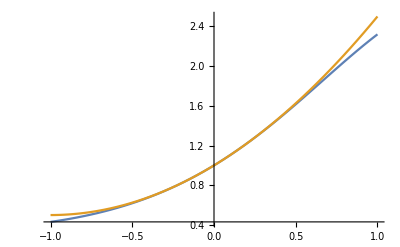

```mathematica
Plot[{f[x],1+x+x^2/2},{x,-1,1}]
```

## 13.- Para aproximar la raíz cúbica de 2, calcular el polinomio de Taylor de grado 3 en el punto 1 de la función raíz cúbica y obtener una aproximación de la raíz cúbica de 2. Julio 23

Solución:
El polinomio de Taylor de grado 3 de una función f(x) en el punto x_0 es f(x_0) + f ‘ (x_0) (x-x_0) + (f''(x_0))/(2!)(x-x_0)^2+ (f'''(x_0))/(3!)(x-x_0)^3
En este caso x_0=1. La función f(x)=x^(1/3) . Calculamos las derivadas
f(x) = x^(1/3)
f ’(x)= (1/3) x^(1/3-1) = (1/3) x^(-2/3)
f’’(x) = -(2/9) x^(-5/3)
f’’’(x) = (10/27) x^(-8/3)

f(1) = 1
f ‘(1)= (1/3) 
f’’(1) = -(2/9) 
f’’’(1) = (10/27)

El polinomio de Taylor es: p(x) = 1 + (1/3) (x-1) - (2/9)/(2!)(x-1)^2+ (10/27)/(3!)(x-1)^3 = 1 + (x-1)/3 - 1/9(x-1)^2+ 5/81 (x-1)^3 . En el punto x=2 vale 1 + 1/3 - 1/9 + 5/81 = (81+27-9+5)/81= 104/81

Con el Mathematica

```mathematica
f[x_]:= x^(1/3)
```

```mathematica
f[1]+f'[1](x-1)+f''[1]/(2!)(x-1)^2 + f'''[1]/(3!)(x-1)^3
```

1+1/3 (-1+x)-1/9 (-1+x)^2+5/81 (-1+x)^3

```mathematica
%/.x->2
```

104/81

## Aproximación por mínimos cuadrados

## 14.- Calcular la función de la forma f(x) = a x^2+b , con a y b números reales, que mejor aproxima, en el sentido de los mínimos cuadrados, los valores (-2,2), (-1,1), (0,0), (1,1) y (2,2). Julio 23

Solución:
Se trata de buscar la función de esa forma 

E(a,b)= (a*(-2)^2+b-2 )^2+(a*(-1)^2+b-1 )^2 + (a*0^2+b-0 )^2 + (a*1^2+b- 1)^2+ (a*2^2+b-2 )^2 =  (4a+b-2 )^2+(a+b-1 )^2 + (b )^2 + (a+b- 1)^2+ (4a+b-2 )^2 = (4a+b-2 )^2+(a+b-1 )^2 + b^2 + (a+b- 1)^2+ (4a+b-2 )^2.

Calculamos las derivadas parciales e igualamos a cero.

∂_a E(a,b) = 2(4a+b-2 )*4+ 2(a+b-1 )  + 2(a+b- 1) + 2(4a+b-2 )*4 = 32a+8b-16 + 2a+2b-2   + 2a+2b- 2 + 32a+8b-16 = 68a+20b-36 
∂_b E(a,b) = 2(4a+b-2 )+ 2(a+b-1 )  + 2b + 2(a+b- 1) + 2(4a+b-2 ) = 8a+2b-4 + 2a+2b-2  + 2 b + 2a+2b- 2 + 8a+2b-4 = 20a+10b-12 

68a+20b-36=0,   17 a + 5 b = 9
20a+10b-12=0,   10 a + 5b = 6
Si restamos las dos ecuaciones 7 a = 3, a = 3/7. 
b= (6-10a)/5=(6-30/7)/5 =(12/7)/5 = 12/35.

```mathematica
p[x_]:=a x^2 + b
```

```mathematica
error[a_,b_]:=(p[-2]-2)^2+(p[-1]-1)^2+(p[0]-0)^2+ (p[1]-1)^2+(p[2]-2)^2
```

```mathematica
Solve[{D[error[a,b],a]==0,D[error[a,b],b]==0},{a,b}]
```

{{a→3/7,b→12/35}}

## Splines

## 10.- Calcular la función spline de grado 2 y clase 1, en los nodos 1, 2, 3 que interpola los datos f(1)=1, f ‘(1)=2, f (2)= -1, f(3)=2. Julio 23

Solución:
Tenemos que buscar un polinomio en el intervalo [1,2] y otro en el [2,3]. Los dos polinomios deben ser de grado menor o igual a dos y deben “unir” con clase 1 en el punto 2 (es decir deben tener el mismo valor en el punto 2 y la misma derivada).
s(x)=Piecewise[{{p1(x) =a+b(x-1)+(c(x-1))^2, 1≤x≤2}, {p2(x)=d+e(x-2)+(f(x-2))^2, 2≤x≤3}}]
Para calcular el polinomio p1(x) usamos los datos: f(1)=1, f ‘(1)=2, f (2)= -1
p1(1)=a+0+0 = 1
p1’(1)=0+b+0 = 2
p1(2)=1+2(2-1)+c*1=-1 ⟹ c=-4

Una vez calculado el polinomio p1(x) = 1 +2(x-1) - 4(x-1)^2, calculamos su derivada en el punto 2, p1’(x) = 2 - 8 (x-1), p1’(2)=-6.
El polinomio p2(x) debe cumplir
p2(2) = d + 0 + 0 = -1
p2’(2) = 0 + e + 0 = -6
p2(3) = -1 - 6(3-2) + f (3-2)^2 = 2  ⟹ f =2+1+6=9

Por tanto, el polinomio p2(x)=-1-6(x-2)+9 (x-2)^2 y tenemos calculada la función spline.

Con el Mathematica

```mathematica
p1[x_]:=a + b (x-1)+ c (x-1)^2
```

```mathematica
p2[x_]:= d + e (x-2) + f (x-2)^2
```

```mathematica
Solve[{p1[1]==1,p1'[1]==2,p1[2]==-1,p2[2]==-1, p1'[2]==p2'[2],p2[3]==2},{a,b,c,d,e,f}]
```

{{a→1,b→2,c→-4,d→-1,e→-6,f→9}}

```mathematica
{p1[x],p2[x]}/.%
```

{{1+2 (-1+x)-4 (-1+x)^2,-1-6 (-2+x)+9 (-2+x)^2}}

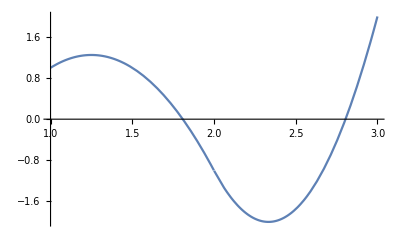

```mathematica
Plot[Which[1≤x≤2,1+2 (-1+x)-4 (-1+x)^2,2≤x≤3,-1-6 (-2+x)+9 (-2+x)^2],{x,1,3}]
```

## Aula de Informática

## 3. Calcular la función del tipo f(x) = a x^2+ bx+c que mejor aproxima en el sentido de los mínimos cuadrados los datos (-2,2), (-1,1), (0,0), (1,-1), (2,0) y (3,1). El sexto decimal de a es: A) 0, B) 2, C) 4, D) 6, E) 8 A) 8, B) 0, C) 2, D) 4, E) 6 El séptimo decimal de a es: A) 9, B) 1, C) 3, D) 5, E) 7 A) 1, B) 3, C) 5, D) 7, E) 9 Aula de Informática. Julio 24

Solución:
Definimos la función error y buscaremos su mínimo:

```mathematica
p[x_]:= a*x^2+ b x + c
```

```mathematica
error[a_,b_,c_]:=(p[-2]-2)^2+ (p[-1]-1)^2+ (p[0]-0)^2+ (p[1]+1)^2+ (p[2]-0)^2+(p[3]-1)^2
```

```mathematica
Solve[{D[error[a,b,c],a]==0,D[error[a,b,c],b]==0,D[error[a,b,c],c]==0},{a,b,c}]
```

{{a→9/28,b→-81/140,c→-8/35}}

```mathematica
N[9/28,20]
```

0.32142857142857142857

El sexto decimal de a es 8. El séptimo decimal de a es 5.

## 6.- Los datos siguientes representan el crecimiento bacterial en un cultivo líquido durante cierto número de días Día | 0 | 4 | 8 | 12 | 16 | 20 Cantidad | 75 | 96 | 110 | 137 | 161 | 197 Usar el polinomio de interpolación para aproximar la cantidad de bacterias que había los días 7 y 14. Polinomio: 75+(21/4+(-7/32+(5/96+(-3/512+(67 (-16+x))/122880) (-12+x)) (-8+x)) (-4+x)) x = 75+(1607 x)/120-(695 x^2)/192+(255 x^3)/512-(85 x^4)/3072+(67 x^5)/122880 Bacterias día 7: 104.932 Bacterias día 14: 149.949 Enero 20. Aula de Informática

```mathematica
InterpolatingPolynomial[{{0,75},{4,96},{8,110},{12,137},{16,161},{20,197}},x]
```

75+(21/4+(-7/32+(5/96+(-3/512+(67 (-16+x))/122880) (-12+x)) (-8+x)) (-4+x)) x

```mathematica
p[x_]:=75+(21/4+(-7/32+(5/96+(-3/512+(67 (-16+x))/122880) (-12+x)) (-8+x)) (-4+x)) x
```

```mathematica
Collect[p[x],x]
```

75+(1607 x)/120-(695 x^2)/192+(255 x^3)/512-(85 x^4)/3072+(67 x^5)/122880

```mathematica
p[7]//N
```

104.932

```mathematica
p[14]//N
```

149.949